```mathematica
ClearAll["Global`*"]
```

```mathematica
(* For the prereheting scenario with inflaton potential , 
(1) we solve numerically the background (inflaton , Hubble ),the daughter mode function  and number density  for different  modes. In the spectator dynamics , we neglet the contribution from universe's expansion.
(2) we find an analytic expression for the inflaton solution and map the spectator field equation to a Mathieu equation like. The resonance parameter  (and  too) depends on time.
(3) As a conseguence of  time-dependence, the resonance bands for  change through time evolution; hence a  mode that starts in a resonance region can exit later in time, implying a non resonance production anymore. We should plot each time the stability/instability chart to see this. *)
```

```mathematica
Mpl=1.0;                    (* reduced mass Planck *)
mϕ=1.0;                      (* inflation mass *)
λ = 1.0;                       (* self-coupling constant *)
g=200.0;                    (* coupling constant ϕ-χ *)
tMax=50.0;               (* time *)
Φ=0.1 Mpl;                (* initial amplitude ϕ *)
```

## Solving Background equations and Spectator equation

```mathematica
(* Background equations: EOM Inflaton field, Friedman equation *)
H[ϕ_,dϕ_]:=√(1/(3 Mpl^2)(1/2 dϕ^2 + 1/2 mϕ^2 ϕ^2+ λ/4 ϕ^4));
eqa = a'[t]==a[t]*H[ϕ[t],ϕ'[t]];
eqϕ=ϕ''[t]+3H[ϕ[t],ϕ'[t]]ϕ'[t]+mϕ^2 ϕ[t]+λ ϕ[t]^3==0;

(*Initial conditions*)
backgroundconditions = {a[0]==1,ϕ[0]==Φ,ϕ'[0]==0};

(* Solve Background dynamic *)
solbackground=NDSolve[{eqϕ,eqa,backgroundconditions[[1]],backgroundconditions[[2]],backgroundconditions[[3]]},{ϕ,a},{t,0,tMax},MaxSteps->Infinity];

(* Solution's background *)
ϕsol[t_]:=Evaluate[ϕ[t]/. solbackground[[1]]];
asol[t_]:=Evaluate[a[t]/. solbackground[[1]]];
Hsol[t_]:=H[ϕsol[t],ϕsol'[t]];
```

```mathematica
(* Frequency *)
ω2[t_,k_]:=k^2+g^2 ϕsol[t]^2;
ω[t_,k_]:=√ω2[t,k];

(* EOM daughter χ *)
eqχ=χ''[t]+ω2[t,k]*χ[t]==0;

(*Initial conditions*)
χconditions={χ[0]==1/(√(2ω[0,k])),χ'[0]==-I*√(ω[0,k]/2)}; (* Initial conditions  to be valued at  *)

(*Solve χ dynamic *)
solχ=ParametricNDSolveValue[{eqχ,χconditions[[1]],χconditions[[2]]},χ,{t,0,tMax},{k},MaxSteps->Infinity,Method->"StiffnessSwitching"];

(* Number density particles *)
numberχ[t_,k_] := Module[{χsolK},
χsolK = solχ[k];
Abs[χsolK'[t]]^2/ω[t,k]+ω[t,k]/2 Abs[χsolK[t]]^2-1/2
];
```

## Evaluate for specific momenta

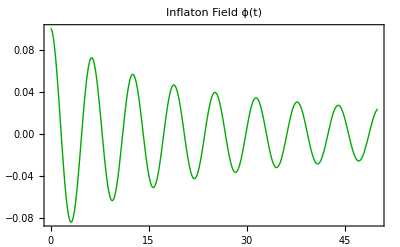

```mathematica
(*Plots *)
aHPlot = Plot[{asol[t],Hsol[t]},{t,0,tMax},PlotRange->All,PlotLegends->{"a(t)","H(t)"},Frame->True,PlotLabel->"Scale factor and Hubble evolution"];
ϕPlot = Plot[ϕsol[t],{t,0,tMax},PlotRange->All,PlotStyle->{Thick,Darker[Green]},Frame->True,PlotLabel->"Inflaton Field ϕ(t)"];
GraphicsGrid[Partition[{aHPlot,ϕPlot},2,2,{1,2},""]]
```

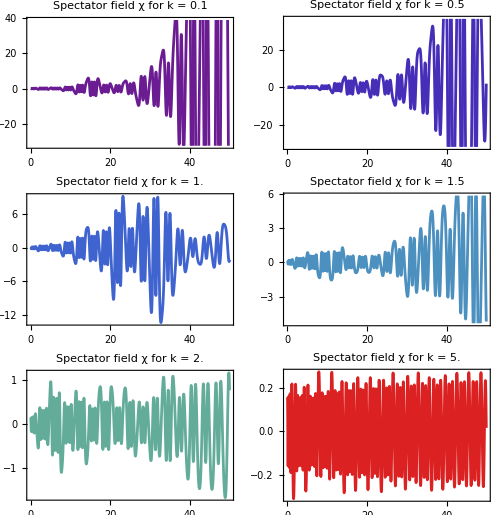

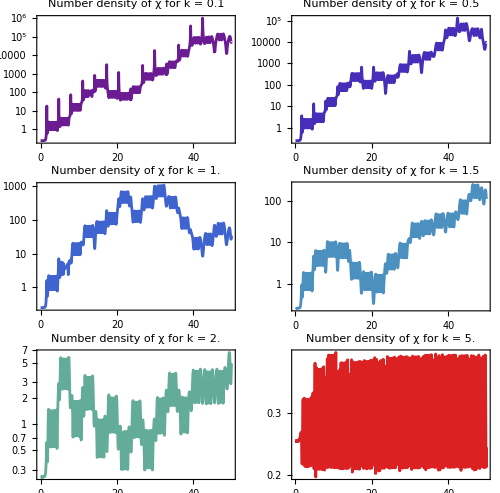

```mathematica
kList={0.1,0.5,1.0,1.5,2.0,5.0};

χKPlot[k_]:=Module[{χsolK},
χsolK = solχ[k];
Plot[Re[χsolK[t]],{t,0,tMax},PlotLabel->Style[StringForm["Spectator field χ for k = ``",k],12],Frame->True,PlotStyle->ColorData["Rainbow"][k/5] ]
];
allχPlots=χKPlot/@kList;
gridχRows=Partition[allχPlots,2,2,{1,1},""];
autoGrid1=GraphicsGrid[gridχRows,ImageSize->500,Spacings->{20,20}]

numberχKPlot[k_]:=LogPlot[numberχ[t,k],{t,0,tMax},PlotLabel->Style[StringForm["Number density of χ for k = ``",k],12],Frame->True,PlotStyle->ColorData["Rainbow"][k/5] ];
allnumberχPlots=numberχKPlot/@kList;
gridnumberχRows=Partition[allnumberχPlots,2,2,{1,1},""];
autoGrid2=GraphicsGrid[gridnumberχRows,ImageSize->500,Spacings->{20,20}]
```

```mathematica
Manipulate[Plot[Re[solχ[k][t]],{t,0,tMax},PlotRange->All,AxesLabel->Automatic,PlotStyle->{Thick,Darker[Blue]},PlotLabel->Style[StringForm["Spectator Field χ_k(z) for different modes k"],14]],{k,0.1,3.0}]

Manipulate[Plot[numberχ[z,k],{z,0,tMax},PlotRange->All,AxesLabel->Automatic,PlotStyle->{Thick,Darker[Blue]},PlotLabel->Style[StringForm["Number density n_k(z) for different modes k"],14]],{k,0.1,3.0}]
```

## Find analytic solution for inflaton field: try

Fit parameters: {θ1→0.0885567,θ2→0.0303726,θ3→1.00119,θ4→1.50719}

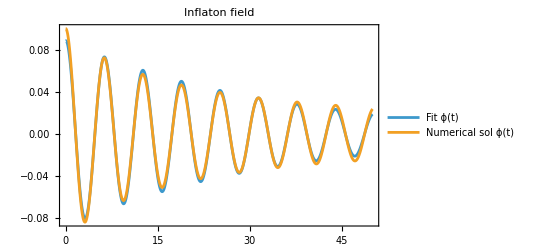

```mathematica
dataϕ=Table[{t,ϕsol[t]},{t,0,tMax,0.001}];

fitϕ=FindFit[dataϕ,θ1*Exp[-θ2*t]*Sin[θ3*t + θ4],{{θ1,1},{θ2,0.01},{θ3,1},{θ4,0}},t];
analyticalϕ[t_]=θ1*Exp[-θ2*t]*Sin[θ3*t+θ4]/. fitϕ;

Print["Fit parameters: ",fitϕ]
Plot[{analyticalϕ[t],ϕsol[t]},{t,0,tMax},PlotRange->All,PlotLegends->{"Fit ϕ(t)","Numerical sol ϕ(t)"},Frame->True,PlotLabel->"Inflaton field"]
```

## Mapping Spectator equation to the Mathieu equation: , ,

```mathematica
(* Parameters *)
q[z_]:=(g^2 θ1^2 Exp[-2 θ2/θ3(z - θ4)])/(4 θ3^2)/.fitϕ //Simplify; (* Resonance parameter *)
A[z_,k_]:= k^2/θ3^2 + 2 q[z] /. fitϕ //Simplify;

(* Mathieu equation for daughter χ *)
eqχMathieu = χ''[z] + (A[z,k] - 2 q[z]Cos[2 z])χ[z]==0;

(*Initial conditions*)
χconditionsM={χ[0]==1/(√(2Sqrt[A[0,k] - 2q[0]])),χ'[0]==-I*√(Sqrt[A[0,k] - 2q[0]]/2)};

(*Solve χ dynamic *)
zMax = θ3*tMax + θ4 /. fitϕ;
solχMathieu=ParametricNDSolveValue[{eqχMathieu,χconditionsM[[1]],χconditionsM[[2]]},χ,{z,0,zMax},{k},MaxSteps->Infinity,Method->"StiffnessSwitching"];
```

## Evaluate the solutions for a specific momentum

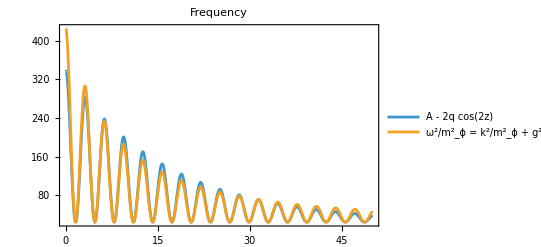

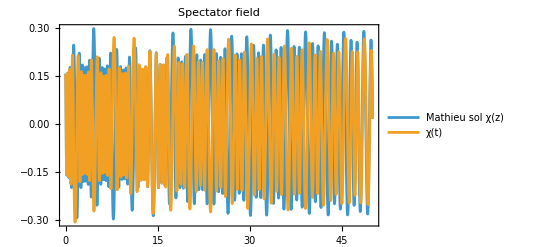

```mathematica
kvalue = 5.0;
χsolK = solχ[kvalue];
χsolMathieuK = solχMathieu[kvalue];

Plot[{A[θ3*t + θ4,kvalue] -2q[θ3*t + θ4]Cos[2 (θ3 t + θ4)]/.fitϕ,ω2[t,kvalue]/mϕ^2},{t,0,tMax},PlotRange->All,Frame->True,PlotLegends->{"A - 2q cos(2z)","ω^2/((m^2)_ϕ) = k^2/((m^2)_ϕ) + g^2/((m^2)_ϕ)ϕ^2(t)"},PlotLabel->"Frequency"]
Plot[{Re[χsolMathieuK[θ3*t + θ4]]/.fitϕ,Re[χsolK[t]]},{t,0,tMax},PlotRange->All,PlotLegends->{"Mathieu sol χ(z)","χ(t)"},Frame->True,PlotLabel->"Spectator field"]
```

## Stability / Instability chart Time evolution

```mathematica
(* Choosing a specific  mode of the spectator field, we plot at different times the instability/stability chart.*) 
zvalues = Range[0,zMax,5];
Kval = 5.0;

qMaxChart = q[zvalues]+50;
AMaxChart = A[zvalues,Kval] + 50;

qPoint = q[zvalues];
APoint = A[zvalues,Kval];
qAPoints = Riffle[qPoint,APoint];

μ[A_,q_]:=Abs[Im[MathieuCharacteristicExponent[A,q]]];
```

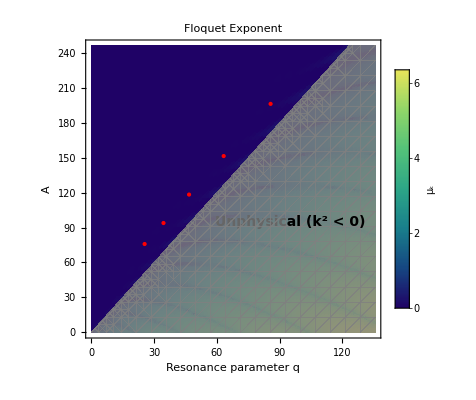

```mathematica
plotFloquet=DensityPlot[μ[A,q],{q,0,Max[qMaxChart]},{A,0,Max[AMaxChart]},PlotPoints->80,MaxRecursion->2,ColorFunction->"BlueGreenYellow",PlotRange->All,PlotLegends->BarLegend[Automatic,LegendLabel->"μ_k"],FrameLabel->{"Resonance parameter q","A"},PlotLabel->"Floquet Exponent"];
unphysicalRegion =RegionPlot[A<2*q,{q,0,Max[qMaxChart]},{A,0,Max[AMaxChart]},BoundaryStyle->None,PlotStyle->Directive[Gray,Opacity[0.8]]];
PointK= ListPlot[{{qAPoints[[1]],qAPoints[[2]]},{qAPoints[[3]],qAPoints[[4]]},{qAPoints[[5]],qAPoints[[6]]},{qAPoints[[7]],qAPoints[[8]]},{qAPoints[[9]],qAPoints[[10]]}},PlotStyle->{Red,PointSize[Large]}];

Show[plotFloquet,PointK,unphysicalRegion,Epilog->Text[Style["Unphysical (k^2 < 0)",Black,Bold,14],{Max[qMaxChart]*0.7,Max[qMaxChart]*0.7}]]
```